# Discrete Mathematics Practical (Semester 3)

## Reflexivity , Anti-Symmetry and Transitivity

```mathematica
pairQ[{_,_}]:= True;
pairQ[___]:= False;
```

```mathematica
relationQ[{__?pairQ}]:= True;
relationQ[___]:= False;
```

## ~Reflexivity

```mathematica
reflexiveQ[R_?relationQ]:= Module[{a,domain},
domain= Union[Flatten[R,1]];
Catch[
Do[If[!MemberQ[R,{a,a}],Throw[False]],{a,domain}];
Throw[True]
]
]
```

```mathematica
reflexiveQ[{{1,1},{2,2},{3,3},{4,4}}]
```

True

```mathematica
reflexiveQ[{{1,1},{2,2},{3,3},{3,4}}]
```

False

Question - Create a relation R = {a, b : aϵA , bϵB and a divides b } (here input is set A)

```mathematica
dividesRelation[A:{__Integer}]:=
Select[Tuples[A,2],Divisible[#[[2]],#[[1]]]&]
```

```mathematica
B={2,3,5,8};
Tuples[B,2]
dividesRelation[B]
```

{{2,2},{2,3},{2,5},{2,8},{3,2},{3,3},{3,5},{3,8},{5,2},{5,3},{5,5},{5,8},{8,2},{8,3},{8,5},{8,8}}

{{2,2},{2,8},{3,3},{5,5},{8,8}}

```mathematica
reflexiveQ[{{2,2},{2,8},{3,3},{5,5},{8,8}}]
```

True

## ~Anti-Symmetry

```mathematica
AntiSymmetricQ[R___?relationQ]:= 
Module[{domain,a,b}, domain = Union[Flatten[R,1]];
Catch
[Do[If[MemberQ[R,{a,b}] && MemberQ[R,{b,a}]&& a ≠ b, 
Throw[False]], {a,domain},{b,domain}];
Throw[True]
]
]
```

```mathematica
A={{1,1},{2,2},{3,3}};
B={{1,1},{2,2},{3,3},{1,4},{4,1}};
AntiSymmetricQ[A]
```

True

```mathematica
AntiSymmetricQ[B]
```

False

## ~Transitivity

```mathematica
TransitiveQ[R__?relationQ]:=
Module[{domain , a ,b , c },domain = Union[Flatten[R,1]];
Catch
[
Do[If[MemberQ[R,{a,b}]&& MemberQ[R,{b,c}]&&
!MemberQ[R,{a,c}],
 Throw[False]], {a,domain},{b,domain} , {c,domain}];
Throw[True]
]
]
```

```mathematica
TransitiveQ[{{1,2},{2,3},{1,3}}]
```

True

```mathematica
TransitiveQ[{{2,2},{2,8},{3,3},{5,5},{8,8}}]
```

True

## PARTIAL ORDER

```mathematica
partialOrderQ[R_?relationQ]:= 
reflexiveQ[R]&& AntiSymmetricQ[R]&&TransitiveQ[R]
```

```mathematica
partialOrderQ[{{2,2},{2,8},{3,3},{5,5},{8,8}}]
```

True

```mathematica
partialOrderQ[A]
```

True

```mathematica
partialOrderQ[B]
```

False

```mathematica
partialOrderQ[{{2,2},{2,8},{3,3},{5,5},{8,8}}]
```

True

```mathematica
partialOrderQ[{{1,1},{2,2},{3,3},{4,4}}]
```

True

## COVERING RELATION

```mathematica
coversQ[R_?partialOrderQ,{x_,y_}]:=
Module[{z,checkSet},
Catch[
If[x==y,Throw[False]];
If[!MemberQ[R,{x,y}],Throw[False]];
checkSet=Complement[Union[Flatten[R,1]],{x,y}];
Do[If[MemberQ[R,{x,z}]&&MemberQ[R,{z,y}],
Throw[False]],
{z,checkSet}];
Throw[True]
]
]
```

```mathematica
r1={{1,1},{1,2},{1,3},{1,4},{2,2},{2,3},{2,4},{3,3},{3,4},{4,4}};
coversQ[r1,{1,2}]
```

True

```mathematica
coversQ[r1,{2,2}]
```

False

```mathematica
coversQ[r1,{1,4}]
```

False

```mathematica
coveringRelation[R_?partialOrderQ]:=
Select[R,coversQ[R,#]&]
```

```mathematica
coveringRelation[r1]
```

{{1,2},{2,3},{3,4}}

```mathematica
P= {1,2,3,4,5};
Tuples[P,2];
coveringRelation[dividesRelation[P]]
```

{{1,2},{1,3},{1,5},{2,4}}

#### ∘Divisor Lattice

```mathematica
divisorLattice[n_Integer]:= dividesRelation[Divisors[n]]
divisorLattice[30]
```

{{1,1},{1,2},{1,3},{1,5},{1,6},{1,10},{1,15},{1,30},{2,2},{2,6},{2,10},{2,30},{3,3},{3,6},{3,15},{3,30},{5,5},{5,10},{5,15},{5,30},{6,6},{6,30},{10,10},{10,30},{15,15},{15,30},{30,30}}

```mathematica
coveringRelation[divisorLattice[30]]
```

{{1,2},{1,3},{1,5},{2,6},{2,10},{3,6},{3,15},{5,10},{5,15},{6,30},{10,30},{15,30}}

#### ∘Power Relation

```mathematica
powerRelation[A:{__Integer}]:=
Select[Tuples[Subsets[A],2],
Intersection[#[[1]],#[[2]]]==#[[1]]&]
```

```mathematica
p1=powerRelation[{1,2}]
```

{{{},{}},{{},{1}},{{},{2}},{{},{1,2}},{{1},{1}},{{1},{1,2}},{{2},{2}},{{2},{1,2}},{{1,2},{1,2}}}

```mathematica
coversQ[p1,{{1},{1,2}}]
```

True

```mathematica
coveringRelation[p1]
```

{{{},{1}},{{},{2}},{{1},{1,2}},{{2},{1,2}}}

### Minimal Elements

```mathematica
minimalElements[R_?partialOrderQ,S_List]:=
Module[{M,s,t},
M=S;
Do[
Do[
If[MemberQ[R,{t,s}],M=Complement[M,{s}]]
,{t,Complement[S,{s}]}]
,{s,S}];
M
]
```

```mathematica
minimalElements[divisorLattice[30],{2,3,6}]
```

{2,3}

```mathematica
B={1,2,3,4,5,6};
div6= dividesRelation[B]
```

{{1,1},{1,2},{1,3},{1,4},{1,5},{1,6},{2,2},{2,4},{2,6},{3,3},{3,6},{4,4},{5,5},{6,6}}

```mathematica
minimalElements[div6,{2,4,6}]
```

{2}

```mathematica
minimalElements[div6,Range[6]]
```

{1}

```mathematica
minimalElements[divisorLattice[60],{10,20,15}]
```

{10,15}

```mathematica
minimalElements[divisorLattice[60],{2,20,15}]
```

{2,15}

```mathematica
minimalElements[divisorLattice[60],{2,3,5}]
```

{2,3,5}

### Maximal Elements

```mathematica
maximalElements[R_?partialOrderQ,S_List]:=
Module[{M,s,t},
M=S;
Do[
Do[
If[MemberQ[R,{s,t}],M=Complement[M,{s}]]
,{t,Complement[S,{s}]}]
,{s,S}];
M
]
```

```mathematica
maximalElements[divisorLattice[30],{2,3,6}]
```

{6}

```mathematica
maximalElements[div6,{2,4,6}]
```

{4,6}

```mathematica
maximalElements[divisorLattice[60],{10,20,15}]
```

{15,20}

```mathematica
maximalElements[div6,Range[6]]
```

{4,5,6}

```mathematica
maximalElements[divisorLattice[60],{2,20,15}]
```

{15,20}

```mathematica
maximalElements[divisorLattice[60],{2,3,5}]
```

{2,3,5}

## UPPER BOUND

```mathematica
upperBoundQ[R_?partialOrderQ,S_List,u_]:=Module[{s},
Catch[
Do[If[!MemberQ[R,{s,u}],Throw[False]]
,{s,S}];
Throw[True]
]
]
```

```mathematica
upperBoundQ[div6,{1,2,3},6]
```

True

```mathematica
upperBoundQ[div6,{1,2,3,4},6]
```

False

```mathematica
upperBounds[R_?partialOrderQ,S_List]:=
Module[{domR,d ,U={}},
domR=Union[Flatten[R,1]];
Do[If[upperBoundQ[R,S,d],AppendTo[U,d]]
,{d,domR}];
U
]
```

```mathematica
upperBounds[div6,{1,2,3}]
```

{6}

```mathematica
upperBounds[divisorLattice[60],{1,2,5,15}]
```

{30,60}

LEAST UPPER BOUND

```mathematica
leastUpperBound[R_?partialOrderQ,S_List]:=
Module[{U,M},
U=upperBounds[R,S];
M=minimalElements[R,U];
If[Length[M]≠1,Null , M[[1]]]
]
```

```mathematica
leastUpperBound[div6,{1,2}]
```

2

## LOWER BOUND

```mathematica
lowerBoundQ[R_?partialOrderQ,S_List,l_]:=Module[{s},
Catch[
Do[If[!MemberQ[R,{l,s}],Throw[False]],
{s,S}];
Throw[True]
]
]
```

```mathematica
lowerBoundQ[div6,{1,2,3},1]
```

True

```mathematica
lowerBoundQ[div6,{1,2,3},4]
```

False

```mathematica
lowerBoundQ[div6,{2,3,4},1]
```

True

```mathematica
lowerBounds[R_?partialOrderQ,S_List]:=
Module[{domR,d ,L={}},
domR=Union[Flatten[R,1]];
Do[If[lowerBoundQ[R,S,d],AppendTo[L,d]]
,{d,domR}];
L
]
```

```mathematica
lowerBounds[div6,{2,6}]
```

{1,2}

GREATEST LOWER BOUND

```mathematica
greatestLowerBound[R_?partialOrderQ,S_List]:=
Module[{U,M},
U=lowerBounds[R,S];
M=maximalElements[R,U];
If[Length[M]≠1,"does not exist",M[[1]]]
]
```

```mathematica
greatestLowerBound[div6,{3,6}]
```

3

```mathematica
greatestLowerBound[div6,{3,5,6}]
```

1

```mathematica
greatestLowerBound[div6,{2,4,6}]
```

2

```mathematica
d66=Complement[div6,{{1,1}}]
```

{{1,2},{1,3},{1,4},{1,5},{1,6},{2,2},{2,4},{2,6},{3,3},{3,6},{4,4},{5,5},{6,6}}

Question 2.1 . Find join and meet :

```mathematica
P={1,2,3,4,5,6,7};
div7=dividesRelation[P]
```

{{1,1},{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{2,2},{2,4},{2,6},{3,3},{3,6},{4,4},{5,5},{6,6},{7,7}}

```mathematica
leastUpperBound[div7,{3}]
```

3

```mathematica
greatestLowerBound[div7,{3}]
```

3

```mathematica
leastUpperBound[div7,{4,6}]
```

```mathematica
greatestLowerBound[div7,{4,6}]
```

2

```mathematica
leastUpperBound[div7,{2,3}]
```

6

```mathematica
greatestLowerBound[div7,{2,3}]
```

1

```mathematica
leastUpperBound[div7,{2,3,6}]
```

6

```mathematica
greatestLowerBound[div7,{2,3,6}]
```

1

```mathematica
leastUpperBound[div7,{1,5}]
```

5

```mathematica
greatestLowerBound[div7,{1,5}]
```

1

Question 2.2 .

```mathematica
d60= dividesRelation[{1,2,4,5,6,12,20,30,60}]
```

{{1,1},{1,2},{1,4},{1,5},{1,6},{1,12},{1,20},{1,30},{1,60},{2,2},{2,4},{2,6},{2,12},{2,20},{2,30},{2,60},{4,4},{4,12},{4,20},{4,60},{5,5},{5,20},{5,30},{5,60},{6,6},{6,12},{6,30},{6,60},{12,12},{12,60},{20,20},{20,60},{30,30},{30,60},{60,60}}

```mathematica
greatestLowerBound[d60,{20,30}]
```

does not exist

```mathematica
leastUpperBound[d60,{2,5}]
```

## HASSE DIAGRAMS

```mathematica
hasseDiagram[R_?partialOrderQ]:=Module[{edges},
edges=coveringRelation[R]/.{a_,b_}->Rule[b,a];
LayeredGraphPlot[edges,VertexLabeling->True]
]
```

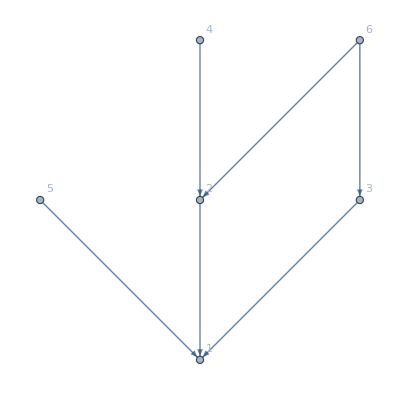

```mathematica
hasseDiagram[div6]
```

```mathematica
divisorLattice[20]
```

{{1,1},{1,2},{1,4},{1,5},{1,10},{1,20},{2,2},{2,4},{2,10},{2,20},{4,4},{4,20},{5,5},{5,10},{5,20},{10,10},{10,20},{20,20}}

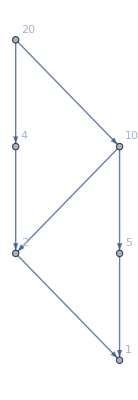

```mathematica
hasseDiagram[divisorLattice[20]]
```

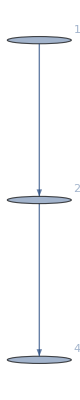

```mathematica
LayeredGraphPlot[{1->2,2->4},VertexLabeling->True]
```

```mathematica
hasLUBs[R_?partialOrderQ]:= Module[{domR,a,b}, 
domR=Union[Flatten[R,1]];
Catch[
Do[If[leastUpperBound[R,{a,b}]=== Null , Throw[False]]
,{a,domR},{b,domR}];
Throw[True]
]
]
```

```mathematica
hasGLBs[R_?partialOrderQ]:= Module[{domR,a,b}, 
domR=Union[Flatten[R,1]];
Catch[
Do[If[greatestLowerBound[R,{a,b}]=== Null ,
 Throw[False]]
,{a,domR},{b,domR}];
Throw[True]
]
]
```

```mathematica
latticeQ[R_?partialOrderQ]:= hasLUBs[R]&& hasGLBs[R]
```

```mathematica
div6
```

{{1,1},{1,2},{1,3},{1,4},{1,5},{1,6},{2,2},{2,4},{2,6},{3,3},{3,6},{4,4},{5,5},{6,6}}

```mathematica
latticeQ[div6]
```

False

```mathematica
p1
```

{{{},{}},{{},{1}},{{},{2}},{{},{1,2}},{{1},{1}},{{1},{1,2}},{{2},{2}},{{2},{1,2}},{{1,2},{1,2}}}

```mathematica
latticeQ[p1]
```

True

```mathematica
latticeQ[divisorLattice[20]]
```

True

### Finding the following for a given boolean polynomial function. 1. Representation of Boolean polynomial function and finding its value when the Boolean variable takes particular values over the Boolean Algebra{0,1}. 2. Display in table form of all possible values of Boolean polynomial function over the Boolean {0,1}.

## Logic Operators ( (&& , ∧ ) AND ,(|| , ∨ ) OR and (¬ , ! ,)NOT)

```mathematica
True||False
```

True

```mathematica
True||True
```

True

```mathematica
False||True
```

True

```mathematica
False||False
```

False

```mathematica
True ∨ False
```

True

```mathematica
True && True
```

True

```mathematica
True&& False
```

False

```mathematica
False&&True
```

False

```mathematica
False&&False
```

False

```mathematica
False ∧ True
```

False

```mathematica
!True
```

False

```mathematica
¬False
```

True

```mathematica
True&& ¬True
```

False

```mathematica
False∨¬False
```

True

```mathematica
¬True ∧ ¬False
```

False

## Representing Boolean Functions

1. f (x, y, z) = xy + yz + zx

```mathematica
f[x_,y_,z_]:= (x∧y)∨ (y∧z)∨ (z∧ x);
f[p,q,r]
```

(p&&q)||(q&&r)||(r&&p)

```mathematica
f[True,False , True]
```

True

```mathematica
f[True,False,True]
```

True

```mathematica
f[True,q,r]
```

q||(q&&r)||r

```mathematica
f[True,q,r]//Simplify
```

q||r

2. g (x, y) = ! (! (x + y) x + ! ! ! y) + xy + x! y

```mathematica
g[x_,y_]:= !((!(x∨y)∧x)∨!!!y)∨(x∧y)∨(x∧!y)
g[False,False]
```

False

```mathematica
g[False,True]
```

True

3. h (x, y, z) = x (! (y + z)) + (xy + ! z) x

```mathematica
h[x_,y_,z_]:= (x∧(!(y∨z)))∨((x∧y)∨!z)∧x;
h[0,0,0]//Simplify
```

False

```mathematica
h[1,0,0]//Simplify
```

True

```mathematica
h[0,1,0]//Simplify
```

False

```mathematica
h[0,0,1]//Simplify
```

False

```mathematica
h[1,1,0]//Simplify
```

True

```mathematica
h[0,1,1]//Simplify
```

False

```mathematica
h[1,0,1]//Simplify
```

False

#### Table Form

1. For Boolean Expression f :

```mathematica
BooleanTable[{p,q,r,f[p,q,r]},{p,q,r}]//TableForm
```

True | True | True | True
True | True | False | True
True | False | True | True
True | False | False | False
False | True | True | True
False | True | False | False
False | False | True | False
False | False | False | False

```mathematica
Boole[BooleanTable[{p,q,r,f[p,q,r]},{p,q,r}]]//TableForm
```

1 | 1 | 1 | 1
1 | 1 | 0 | 1
1 | 0 | 1 | 1
1 | 0 | 0 | 0
0 | 1 | 1 | 1
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 0

```mathematica
TableForm[Boole[BooleanTable[{p,q,r,f[p,q,r]},{p,q,r}]],
TableHeadings->{None,{p,q,r,f}}]
```

p | q | r | f
1 | 1 | 1 | 1
1 | 1 | 0 | 1
1 | 0 | 1 | 1
1 | 0 | 0 | 0
0 | 1 | 1 | 1
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 0

2. For Boolean expression g:

```mathematica
BooleanTable[{p,q,g[p,q]},{p,q}]//TableForm
```

True | True | True
True | False | True
False | True | True
False | False | False

```mathematica
Boole[BooleanTable[{p,q,g[p,q]},{p,q}]]//TableForm
```

1 | 1 | 1
1 | 0 | 1
0 | 1 | 1
0 | 0 | 0

```mathematica
TableForm[Boole[BooleanTable[{p,q,g[p,q]},{p,q}]],
TableHeadings->{None,{p,q,g}}]
```

p | q | g
1 | 1 | 1
1 | 0 | 1
0 | 1 | 1
0 | 0 | 0

3. For Boolean expression h :

```mathematica
BooleanTable[{p,q,r,h[p,q,r]},{p,q,r}]//TableForm
```

True | True | True | True
True | True | False | True
True | False | True | False
True | False | False | True
False | True | True | False
False | True | False | False
False | False | True | False
False | False | False | False

```mathematica
Boole[BooleanTable[{p,q,r,h[p,q,r]},{p,q,r}]]//TableForm
```

1 | 1 | 1 | 1
1 | 1 | 0 | 1
1 | 0 | 1 | 0
1 | 0 | 0 | 1
0 | 1 | 1 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 0

```mathematica
TableForm[Boole[BooleanTable[{p,q,r,h[p,q,r]},{p,q,r}]],
TableHeadings->{None,{p,q,r,h}}]
```

p | q | r | h
1 | 1 | 1 | 1
1 | 1 | 0 | 1
1 | 0 | 1 | 0
1 | 0 | 0 | 1
0 | 1 | 1 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 0

#### Finding the following: 1. Dual of a Boolean Polynomial/expression. 2. Whether or not two Boolean polynomials are equivalent. 3. Disjunctive normal form( Conjunctive Normal Form)from a given Boolean expression. 4. Disjunctive normal form( Conjunctive Normal Form) when the Boolean polynomial expressed by a table of values.

1. Dual of a Boolean Polynomial/expression .

```mathematica
f[x_,y_,z_]:= (x∧y)∨(y∧z)∨(z∧x)
dual[exp_]:=exp/.{And->Or,Or->And,Ture->False,False->True}
d[x_,y_,z_]=dual[f[x,y,z]]
```

(x||y)&&(y||z)&&(z||x)

```mathematica
%//Simplify
```

(x&&(y||z))||(y&&z)

```mathematica
TableForm[Boole[BooleanTable[{p,q,r,d[p,q,r] , f[p,q,r]},{p,q,r}]],
TableHeadings->{None,{p,q,r,d,f}}]
```

p | q | r | d | f
1 | 1 | 1 | 1 | 1
1 | 1 | 0 | 1 | 1
1 | 0 | 1 | 1 | 1
1 | 0 | 0 | 0 | 0
0 | 1 | 1 | 1 | 1
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0

Ques. Representing a given circuit diagram ( expressed using gates) in the form of Boolean expressions.
To give Boolean expression of the given circuit diagram , we define each gate separately , and finally ask for the value of output G1.

```mathematica
G4= ¬a;
```

```mathematica
G5=¬c;
```

```mathematica
G2= a ∧ b ;
```

```mathematica
G3=G4 ∧ G5 ∧ b ;
```

```mathematica
G1 = G2 ∨ G3;
```

```mathematica
G1
```

(a&&b)||(!a&&!c&&b)

2. Gate Diagram

```mathematica
G2=a∧ b ∧ c ;
```

```mathematica
G4=¬c;
```

```mathematica
G3= a ∧ b ∧ G4 ;
```

```mathematica
G5= ¬a;
```

```mathematica
G6= ¬c;
```

```mathematica
G7= G5 ∧ G6 ∧ b ;
```

```mathematica
G1= G2 ∨ G3 ∨ G7 ;
```

```mathematica
G1
```

(a&&b&&c)||(a&&b&&!c)||(!a&&!c&&b)

Ques . Minimize a given Boolean expression to find minimal expressions . 
To obtain minimised expressions in DNF , we can use booleanMinimize.

```mathematica
BooleanMinimize[(a∧b)∨(!a∧b ∧ !c)]
```

(a&&b)||(b&&!c)

To obtain minimized expression in CNF , we can use BooleanMinimize with specification for CNF as under

```mathematica
BooleanMinimize[(a∧b)∨(!a∧b∧!c),"CNF"]
```

(a||!c)&&b

To obtain minimized expression in whichever form as minimum length , we can use simplify

```mathematica
Simplify [(a∧b)∨ (!a∧b∧!c)]
```

(a||!c)&&b